```mathematica
<<MaTeX`
Unprotect[MaTeX`Developer`Texify];
MaTeX`Developer`Texify[TextCell[code_,___]]:=ToString[code]
M[exp_]:=MaTeX[exp,Magnification->2]
Msoln[exp_]:=MaTeX[If[ToString[TeXForm[exp]]==ToString[TeXForm[FullSimplify[ReleaseHold[exp]]]],ToString[TeXForm[exp]],ToString[TeXForm[exp]]<>"\\,=\\,"<>ToString[TeXForm[FullSimplify[ReleaseHold[exp]]]]]<>If[NumberQ[N[ReleaseHold[exp],5]],"\\,\\approx\\,"<>ToString[TeXForm[N[ReleaseHold[exp],5]]],""],Magnification->2]
```

```mathematica
texStyle={FontFamily->"Times New Roman",FontSize->12};
```

Noise analysis from satellite data

```mathematica
(*Format of the satellite data: {Epoch time (J2000 seconds),0 for some reason, clock data in (meters)
formal error in (meters) SVN name}*)
```

```mathematica
(*Import Satellite Data*)
data=Import["D:\\academics university\\2022 Spring\\NSERC project\\2017-08-14_hr.tdp", "Data"]
```

{{555930000,0.00191986,0.00191986,0.000174533,.Satellite.GPS73.Models.AttitudeModel.YawRate},{555930000,0.,10862.6,0.186496,.Satellite.GPS73.Clk.Bias},{555930000,0.00191986,0.00191986,0.000174533,.Satellite.GPS72.Models.AttitudeModel.YawRate},6695719,{556038000,0.,-24236.2,0.132619,.Satellite.GPS41.Clk.Bias},{556038000,0.00221657,0.00221657,0.000174533,.Satellite.GPS36.Models.AttitudeModel.YawRate},{556038000,0.,3037.67,0.229644,.Satellite.GPS36.Clk.Bias}}
 |  |  |  |

```mathematica
(*Dump Save*)
DumpSave["data.mx", data]
```

{{{555930000,0.00191986,0.00191986,0.000174533,.Satellite.GPS73.Models.AttitudeModel.YawRate},{555930000,0.,10862.6,0.186496,.Satellite.GPS73.Clk.Bias},6695722,{556038000,0.,3037.67,0.229644,.Satellite.GPS36.Clk.Bias}}}
 |  |  |  |

```mathematica
(*You can recover data here*)
<<data.mx
```

```mathematica
Global`data
```

{{555930000,0.00191986,0.00191986,0.000174533,.Satellite.GPS73.Models.AttitudeModel.YawRate},{555930000,0.,10862.6,0.186496,.Satellite.GPS73.Clk.Bias},6695721,{556038000,0.00221657,0.00221657,0.000174533,.Satellite.GPS36.Models.AttitudeModel.YawRate},{556038000,0.,3037.67,0.229644,.Satellite.GPS36.Clk.Bias}}
 |  |  |  |

```mathematica
(*Sort data*)
dataSorted=
SortBy[(*Sort the elements by Satellite name*)
GatherBy[(*Partition the list by Satellite name*)
ReplaceAll[(*Replaces all of the " .Satellite.GPSXX.Clk.Bias" strings with just the SVN Name GPSXX*)
Cases[(*This function finds and removes all instances of YawRate data. We don't need any of these*)
data
,_?(StringFreeQ[#[[5]],".Satellite.GPS"~~__~~".Models.AttitudeModel.YawRate"]&)
]
, s_String:> StringReplace[s,".Satellite."~~x__~~".Clk.Bias":>x]]
,Last]
,#[[1,5]]&]
```

{1}
 |  |  |  |

```mathematica
(*Dump save sorted dara*)
DumpSave["dataSorted.mx", dataSorted]
```

{{1}}
 |  |  |  |

```mathematica
(*You can recover data here*)
<<dataSorted.mx
```

```mathematica
Global`dataSorted
```

{{{555930000,0.,2859.57,0.190685,GPS36},{555930001,0.,2859.58,0.190686,GPS36},{555930002,0.,2859.58,0.190687,GPS36},{555930003,0.,2859.58,0.190688,GPS36},107994,{556037998,0.,3037.67,0.229617,GPS36},{556037999,0.,3037.67,0.229631,GPS36},{556038000,0.,3037.67,0.229644,GPS36}},29,{1}}
 |  |  |  |

```mathematica
(*A function that takes the time series of a satellite*)
timeseries[lst_]:= Map[Extract[lst[[#]], 3]&, Range[1,10801 ]]
```

```mathematica
(*test*)
```

```mathematica
timeseries36 = timeseries[dataSorted[[1]]];
```

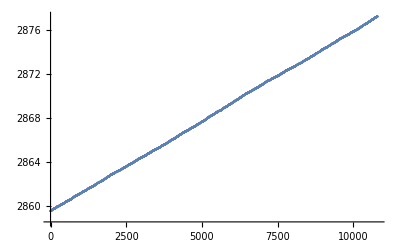

```mathematica
ListPlot[timeseries36]
```

```mathematica
(*a straight line, as expected*)
```

```mathematica
(*Power Spectral Density Functions*)
```

```mathematica
satellitespectal[n_]:= (Transpose@{Range[1, 10701]/10701 ,MovingAverage[Fourier[Differences[timeseries[dataSorted[[n]]]], FourierParameters->{1, -1}]*Conjugate[Fourier[Differences[timeseries[dataSorted[[n]]]], FourierParameters->{1, -1}]], 100]})[[2;;5350]]
```

```mathematica
satellitespectallst[n_]:= MovingAverage[Fourier[Differences[timeseries[dataSorted[[n]]]], FourierParameters->{1, -1}]*Conjugate[Fourier[Differences[timeseries[dataSorted[[n]]]], FourierParameters->{1, -1}]], 100]
```

```mathematica
(*take the mean to reduce the impact of singularity*)
```

```mathematica
mean = (Transpose@{Range[1, 10701]/10701,1/Sqrt[Mean[1/Map[satellitespectallst, Range[21, 31]]^2]]})[[2;;5350]];
```

```mathematica
(*Plot of the mean power spectral density*)
```

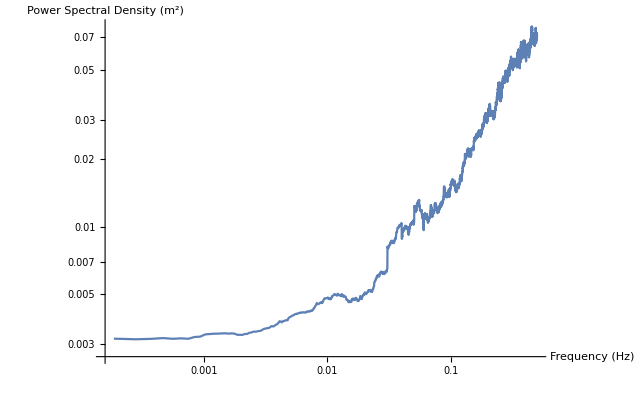

```mathematica
ListPlot[mean,  PlotRange->Full, AxesLabel->{HoldForm["Frequency (Hz)"],HoldForm["Power Spectral Density (m^2)" ]}, Joined->True,BaseStyle->texStyle, LabelStyle->{Black,14}, ScalingFunctions->{"Log", "Log"}]
```

```mathematica
(*Plot of the power spectral density for some selected sample satellites*)
```

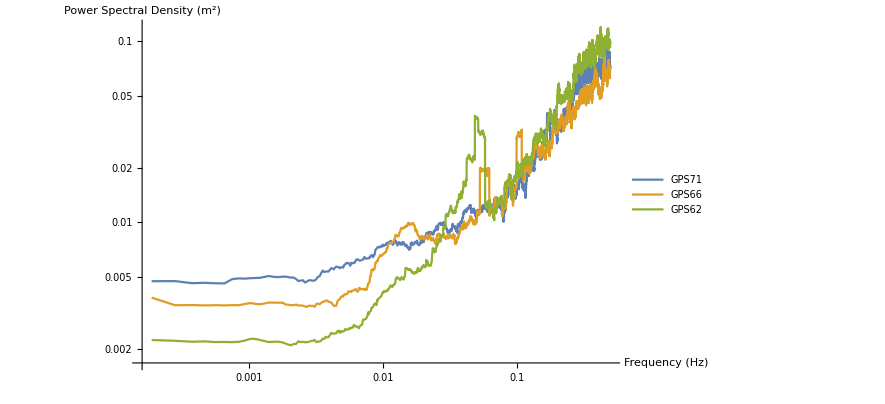

```mathematica
ListPlot[{satellitespectal[29], satellitespectal[25], satellitespectal[21]},AxesLabel->{HoldForm["Frequency (Hz)"],HoldForm["Power Spectral Density (m^2)" ]}, Joined->True,PlotLegends->{"GPS71","GPS66", "GPS62" }, BaseStyle->texStyle, LabelStyle->{Black,14}, ScalingFunctions->{"Log", "Log"}]
```

Theoretical predictions of the wave form

```mathematica
(*constants*)
(*distance to the event*)R:= 1.234271032 *10^(24) (*me*)
(*speed of light*)c:= 299792458. (*me/s*)
(*plank's constant*)h:= 1.054571817×10^(−34) (*kg*me^2/s*)
(*typical ELF mass*) (*m:= 9.78*10^(-50-6) kg*) m:= mass (* kg*)
(*chirp mass*) M:= 1*1.9891*10^(30) (*kg*)
(*gravitational constant*)G:= 6.67*10^(-11) (*me^3/kg / s^2*)
$Assumptions = me>0 && kg >0 && s>0
```

me>0&&kg>0&&s>0

```mathematica
(*wave phase*)
```

```mathematica
Ψ[f_, t_, r_]:= Simplify[I*r*(Sqrt[(2*Pi *f/c)^2-(m*c/h)^2] - 2*Pi*f/c) - 2*I *Pi *f*t + (3*I/128) *(Pi*M *G *f/c^3)^(-5/3)]/.mass->  9.78*10^(-56)
```

```mathematica
(*saddle points (derivative of phase with respect to frequency)*)
```

```mathematica
Clear[g];g[f_, r_] := (-(5 M*(G/c^3))/(256 (f M*(G/c^3))^(8/3) π^(8/3))+((-(2 π)/c+(4 f π^2)/(c^2 √(-(c^2 m^2)/h^2+(4 f^2 π^2)/c^2))) r)/(2 π))
```

```mathematica
(*Using saddle point approximations, a typical wave form looks like this in the time-frequency space*)
```

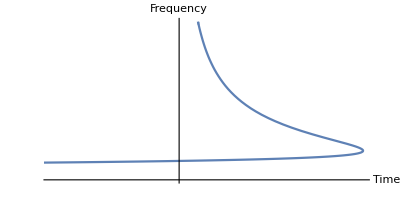

```mathematica
ParametricPlot[{Simplify[g[f,R]/.mass->9.78/10^56],f},{f,0.1,20},AxesLabel->{HoldForm[Time],HoldForm[Frequency]},BaseStyle->texStyle,
 AspectRatio->1/2, Ticks->None, LabelStyle->{Black,14}]
```

```mathematica
(*How the wave form changes with respect to the mass of the scalar field （Log-Log plot）*)
waveformmass=Animate[ParametricPlot[{Log10[(g[f, 1.234271032 *10^(24)])/.mass->x//Simplify],Log10[f]}, {f, 0.01, 5} , PlotPoints->15,PlotRange->{{0, 8}, {-1, 1}}, MaxRecursion->8,AspectRatio->1/3, Ticks->None, AxesLabel->{HoldForm[log[Time]],HoldForm[log[Frequency]]}], {x,5*10^(-56),5*10^(-55) ,0.1*10^(-57)} ]
```

```mathematica
Export["waveform_mass.gif", waveformmass]
```

waveform_mass.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["waveform_mass.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["waveform_mass.gif"]]]
```

```mathematica
(*How the wave form changes with respect to the distance to the event （Log-Log plot）*)
```

```mathematica
waveformdistance = Animate[ParametricPlot[{Log10[(g[f, x])/.mass->9.78*10^(-56)//Simplify],Log10[f]}, {f, 0.01, 5} , PlotPoints->15,PlotRange->{{0, 10}, {-1, 1}}, MaxRecursion->8,AspectRatio->1/3, Ticks->None, AxesLabel->{HoldForm[log[Time]],HoldForm[log[Frequency]]}], {x,0.5*10^(24), 10*10^(24)}]
```

```mathematica
Export["waveform_distance.gif", waveformdistance]
```

waveform_distance.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["waveform_distance.gif"]]]
```

```mathematica
(*new R to let the signal fit in the sampling window*)
(*R= 7.47775*10^24*)
```

```mathematica
(*The exact wave form can not be evaluated analytically. We will use the following saddle point approximation.*)  (*note that we use a different ELF mass here to let the signal fit in the sampling window*)
```

```mathematica
sol[t_]:=  f/.#&/@NSolve[(g[f, R]/.mass-> 2.622*10^(-55))== t,f, Reals]
```

```mathematica
firstsol[t_]:= sol[t][[2]]
```

```mathematica
secondsol[t_]:= sol[t][[3]]
```

```mathematica
approximatephase1[t_]:= Ψ[firstsol[t], t, R] + (1/2 * D[D[Ψ[f, t, R],f],f]/.f-> firstsol[t])*(f- firstsol[t])^2
```

```mathematica
approximatephase2[t_]:= Ψ[secondsol[t], t, R] + (1/2 * D[D[Ψ[f, t, R],f],f]/.f-> secondsol[t])*(f-  secondsol[t])^2
```

```mathematica
waveamplitude1[t_]:=1/firstsol[t]^(7/6) * Exp[Ψ[firstsol[t], t, R]] *1/Sqrt[D[D[Ψ[f, t, R],f],f]/.f-> firstsol[t]]
```

```mathematica
waveamplitude2[t_]:= 1/secondsol[t]^(7/6) * Exp[Ψ[secondsol[t], t, R]] *1/Sqrt[ D[D[Ψ[f, t, R],f],f]/.f-> secondsol[t]]
```

```mathematica
amplitude[t_]:=Which[ Length[NSolve[(((g[f, R])/.mass->2.622*10^(-55))//Simplify) == t,f, Reals]]==2, waveamplitude1[t], 
Length[NSolve[(((g[f, R])/.mass->2.622*10^(-55))//Simplify) == t,f, Reals]]==3, waveamplitude1[t]+waveamplitude2[t], True, 0]
```

Signal-noise ratio calculations

```mathematica
(*Here we use the data processing methods presented in Anderson,W.G.et al.Excess power statistic for detection of burst sources of gravitational radiation.Physical Review D 63,042003 (2001).*)
```

```mathematica
(*We conduct DFT on the noise first. We use the data of satellite 70 as an example.*)
data71=Differences[timeseries[dataSorted[[29]]]]
```

{0.00663479,0.00596651,0.00129434,0.00334376,0.00227106,0.00059757,0.00188103,0.00628943,0.00262427,0.00145487,10780,0.00215358,0.000795587,0.00299597,0.00136888,0.00138768,0.0047804,0.000268749,0.00342333,0.00363759,0.000713566}
 |  |  |  |

```mathematica
(*Plot of the noise*)
```

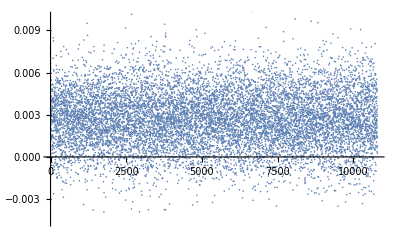

```mathematica
ListPlot[data71]
```

```mathematica
(*DFT of the noise*)
```

```mathematica
DFTdata71 = ShortTimeFourier[data71, FourierParameters->{1, -1}]["Data"]
```

{{0.707062+0. ⅈ,0.00386106-0.00189954 ⅈ,0.0065773+0.00311181 ⅈ,0.0146539-0.0113156 ⅈ,-0.00804275+0.000168164 ⅈ,247,-0.00804275-0.000168164 ⅈ,0.0146539+0.0113156 ⅈ,0.0065773-0.00311181 ⅈ,0.00386106+0.00189954 ⅈ},126,{0.191929+1,255}}
 |  |  |  |

```mathematica
DFTdata71conj = Conjugate[DFTdata71]
```

{{0.707062+0. ⅈ,0.00386106+0.00189954 ⅈ,0.0065773-0.00311181 ⅈ,0.0146539+0.0113156 ⅈ,-0.00804275-0.000168164 ⅈ,247,-0.00804275+0.000168164 ⅈ,0.0146539-0.0113156 ⅈ,0.0065773+0.00311181 ⅈ,0.00386106-0.00189954 ⅈ},126,{0.191929+1,255}}
 |  |  |  |

```mathematica
(*This is the power spectral density (PSD) of the sensor noise*)
```

```mathematica
Cp = Mean[Mean[DFTdata71*DFTdata71conj]]
```

0.00286203+0. ⅈ

```mathematica
(*To convert the wave amplitude into the dimension of m, we need to multiply it by (G M)^(5/6)c^(-3/2) *)
```

```mathematica
dimenamplitude[t_] :=(G M)^(5/6)*c^(-3/2)*amplitude[t]
```

```mathematica
(*test*)
```

```mathematica
dimenamplitude[17.8697*10^6]
```

0.739342

```mathematica
(*Here is a sample signal using the wave amplitude function, from t = 2000 to t = 6500*)
```

```mathematica
samplesignal=Map[dimenamplitude, Range[3000, 6500]];
```

$Aborted

```mathematica
(*Dump save*)
```

```mathematica
DumpSave["samplesignal.mx", samplesignal];
```

```mathematica
(*You can recover the data here*)
```

```mathematica
<<samplesignal.mx
```

```mathematica
Global`samplesignal;
```

```mathematica
(*a plot of the simulated signal*)
```

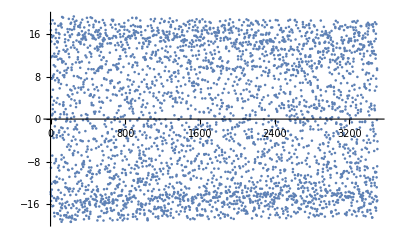

```mathematica
ListPlot[samplesignal]
```

```mathematica
(*DFT of sample signal*)
```

```mathematica
DFTsignal=ShortTimeFourier[samplesignal/(1/Pi^(2/3)*Sqrt[5/24]), FourierParameters->{1, -1}]["Data"]
```

{{182.143+0. ⅈ,-173.151-109.217 ⅈ,-208.634-277.501 ⅈ,-63.9393-226.187 ⅈ,-196.786+116.835 ⅈ,-43.799-304.35 ⅈ,77.778-491.668 ⅈ,114,22.0266+381.556 ⅈ,77.778+491.668 ⅈ,-43.799+304.35 ⅈ,-196.786-116.835 ⅈ,-63.9393+226.187 ⅈ,-208.634+277.501 ⅈ,-173.151+109.217 ⅈ},{1},79,{1}}
 |  |  |  |

```mathematica
DFTsignalconj = Conjugate[DFTsignal]
```

{{182.143+0. ⅈ,-173.151+109.217 ⅈ,-208.634+277.501 ⅈ,-63.9393+226.187 ⅈ,-196.786-116.835 ⅈ,-43.799+304.35 ⅈ,77.778+491.668 ⅈ,114,22.0266-381.556 ⅈ,77.778-491.668 ⅈ,-43.799-304.35 ⅈ,-196.786+116.835 ⅈ,-63.9393-226.187 ⅈ,-208.634-277.501 ⅈ,-173.151-109.217 ⅈ},{1},79,{1}}
 |  |  |  |

```mathematica
(*Amplitude of the signal assuming amplitude is 1.*)
ampsignal =Mean[Mean[DFTsignal * DFTsignalconj]]
```

405250.+0. ⅈ

```mathematica
(*signal-noise ratio*)
(ampsignal/Cp)*A^2
```

(2.55755×10^8+0. ⅈ) A^2

```mathematica
(*A spectrogram of noise + signal*)
```

```mathematica
Spectrogram[data70[[1;;3501]] + samplesignal]
```

-Graphics-

```mathematica
(*frequncy distribution of power*)
```

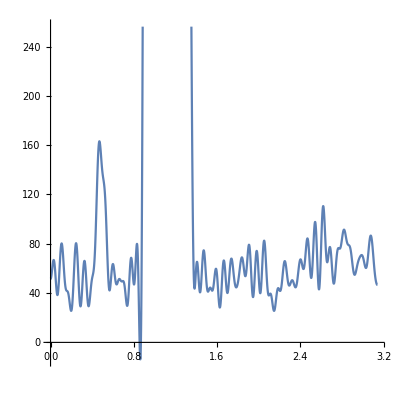

```mathematica
Plot[PowerSpectralDensity[samplesignal+data70[[1;;3501]] , ω, 100], { ω, 0, Pi}, AspectRatio->1]
```

```mathematica
(*another sample signal*)
```

```mathematica
samplesignal2 = Map[dimenamplitude, Range[6619600, 6622600]];
```

$Aborted

```mathematica
(*Dumpsave*)
```

```mathematica
DumpSave["samplesignal2.mx", samplesignal2];
```

```mathematica
(*You can recover data here*)
```

```mathematica
<<samplesignal2.mx
```

```mathematica
Global`samplesignal2;
```

```mathematica
(*Plot of the data*)
```

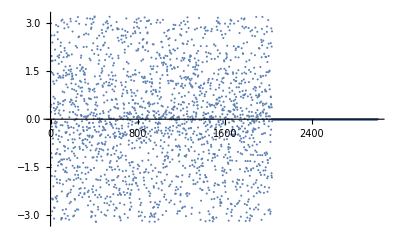

```mathematica
ListPlot[samplesignal2]
```

```mathematica
(*Spectrogram of data + noise*)
```

```mathematica
Spectrogram[data70[[1;;3001]] + samplesignal2]
```

-Graphics-

```mathematica
(*pretty noisy, no signal curve is visible*)
```

```mathematica
(*frequncy distribution of power*)
```

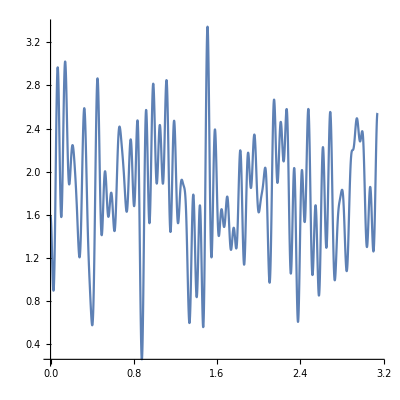

```mathematica
Plot[PowerSpectralDensity[samplesignal2+data70[[1;;3001]] , ω, 100], { ω, 0, Pi}, AspectRatio->1]
```

```mathematica
(*the third sample signal*)
samplesignal3 = Map[dimenamplitude, Range[9018000, 9021000]];
```

$Aborted

```mathematica
(*Dump save*)
```

```mathematica
DumpSave["samplesignal3.mx", samplesignal3];
```

```mathematica
(*you can recover data here*)
```

```mathematica
<<samplesignal3.mx
```

```mathematica
Global`samplesignal3;
```

```mathematica
(*spectrogram of signal + noise*)
```

```mathematica
Spectrogram[data70[[1;;3001]] + samplesignal3]
```

-Graphics-

```mathematica
(*frequncy distribution of power*)
```

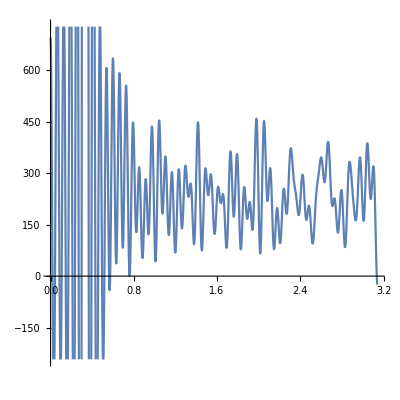

```mathematica
Plot[PowerSpectralDensity[samplesignal3+data70[[1;;3001]] , ω, 100], { ω, 0, Pi}, AspectRatio->1]
```

```mathematica
(*the fourth sample signal*)
samplesignal4 = Map[dimenamplitude, Range[17867000, 17870000]];
```

```mathematica
DumpSave["samplesignal4.mx", samplesignal4];
```

```mathematica
<<samplesignal4.mx
```

```mathematica
Global`samplesignal4;
```

```mathematica
Spectrogram[data70[[1;;3001]] + samplesignal4]
```

-Graphics-

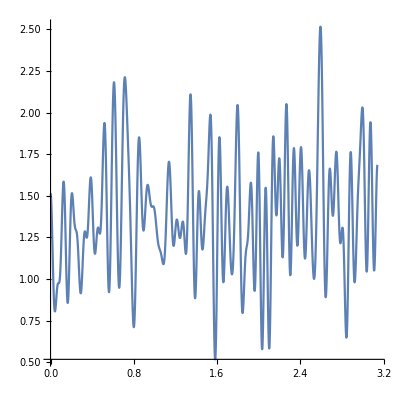

```mathematica
Plot[PowerSpectralDensity[samplesignal4+data70[[1;;3001]] , ω, 100], { ω, 0, Pi}, AspectRatio->1]
```

```mathematica
(*power spectal density of the signal over an observation time T, using numerical integration*)
```

```mathematica
(*integrand*)
```

```mathematica
powerintegrand[ω_, T_, x_]:= 1/ω^(7/6) *Exp[I*3/128 * (M*G* ω/(2*c^3))^(-5/3)+I*Sqrt[(ω/c)^2-(m*c/h)^2] *R]*T*Sinc[1/2 *T *(x - ω)]/.mass->  9.78*10^(-56)
```

```mathematica
(*power spectal density*)
```

```mathematica
powerdist[ω_, T_]:=Abs[ NIntegrate[powerintegrand[x, T, ω], {x, -Infinity, Infinity}, Method->"ExtrapolatingOscillatory"]]^2
```

```mathematica
(*test*)
```

```mathematica
powerdist[50, 30000000]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {0.000818004} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.00767271+0.0541867 ⅈ 和 0.184502.

0.00299507

```mathematica
(*plot of the power spectal density, compared with the curve with infinite observation time*)
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {0.00238361} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -547.897+1871.97 ⅈ 和 5680.43.

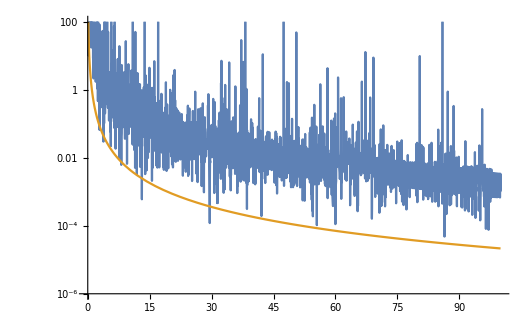

```mathematica
LogPlot[{powerdist[x, 30000000], Abs[1/x^(7/6)]^2}, {x, 0, 100}, PlotRange->{{0, 100}, {10^(-6), 100}}]
```

```mathematica
(*doesn't look quite right. this is probably due to the errors in numerical integration*)
```

```mathematica
(*We seek to evaluate the above integral by saddle point approximations. We transform the sinc function into exponential. Then, the integral becomes the difference of two integrals.*)
(*phases of the two integrals*)
phase1[ω_, ω1_, T_, x_] := I *(3/128 *(M*G*ω1/(2*c^3))^(-5/3) + (R*Sqrt[(ω1/c)^2 - (m*c/h)^2] -R*ω1/c)+ 1/2 *T *(ω-ω1))/.mass-> x(*9.78*10^(-56)*)
phase2[ω_, ω1_, T_, x_] := I *(3/128 *(M*G*ω1/(2*c^3))^(-5/3) + (R*Sqrt[(ω1/c)^2 - (m*c/h)^2]-R*ω1/c) - 1/2 *T *(ω-ω1))/.mass-> x (*9.78*10^(-56)*)
```

```mathematica
(*find the saddle point*)
```

```mathematica
saddlept1[T_, x_]:= (ω1/.#&/@FindRoot[D[ phase1[ω, ω1, T, x], ω1] == 0, {ω1, 0.002}, WorkingPrecision->30])[[1]]
```

```mathematica
saddlept2[T_, x_]:= (ω1/.#&/@FindRoot[D[ phase2[ω, ω1, T, x], ω1] == 0, {ω1, 0.002}, WorkingPrecision->30])[[1]]
```

```mathematica
(*finally, the power spectral density*)
```

```mathematica
(*quadrupole*)
```

```mathematica
approxpowerdistq[ω_, T_, x_]:= Abs[((2*Pi)^(7/6)/(I*(ω - saddlept1[T,x])*saddlept1[T, x]^(7/6)) *Exp[phase1[ω, ω1, T, x]/.ω1->  saddlept1[T, x]]*1/Sqrt[D[D[phase1[ω, ω1, T, x] ,ω1 ], ω1]/.ω1->  saddlept1[T, x]] )- ((2*Pi)^(7/6)/(I*(ω - saddlept2[T, x])*saddlept2[T, x]^(7/6))* Exp[phase2[ω, ω1, T, x]/.ω1->  saddlept2[T, x]]*1/Sqrt[D[D[phase2[ω, ω1, T, x] ,ω1 ], ω1]/.ω1->  saddlept2[T, x]])]^2
```

```mathematica
(*dipole*)
```

```mathematica
approxpowerdistd[ω_, T_, x_]:= Abs[((2*Pi)^(5/6)/(I*(ω - saddlept1[T,x])*(G*M)^(1/3)*saddlept1[T, x]^(3/2)) *Exp[phase1[ω, ω1, T, x]/.ω1->  saddlept1[T, x]]*1/Sqrt[D[D[phase1[ω, ω1, T, x] ,ω1 ], ω1]/.ω1->  saddlept1[T, x]] )- ((2*Pi)^(5/6)/(I*(ω - saddlept2[T, x])*(G*M)^(1/3)*saddlept2[T, x]^(3/2))* Exp[phase2[ω, ω1, T, x]/.ω1->  saddlept2[T, x]]*1/Sqrt[D[D[phase2[ω, ω1, T, x] ,ω1 ], ω1]/.ω1->  saddlept2[T, x]])]^2
```

```mathematica
(*plots of the power spectal density, compared with the curve with infinite observation time*)
```

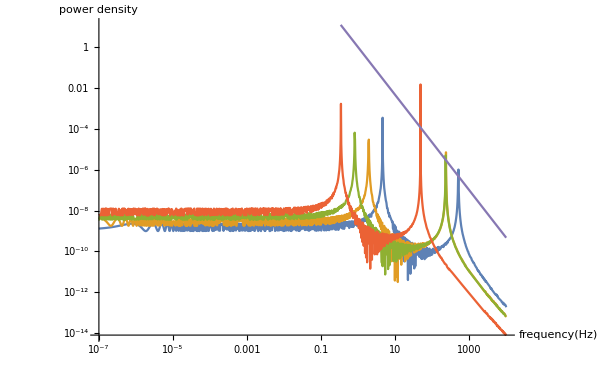

```mathematica
LogLogPlot[{approxpowerdistq[x, 3000000, 0], approxpowerdistq[x, 30000000, 0], approxpowerdistq[x, 300000000, 0], approxpowerdistq[x, 3000000000, 0], Abs[1/x^(7/6)]^2}, {x, 10^(-7), 10000}, PlotRange->{{10^(-7), 10000}, Automatic}, PlotPoints->20, AxesLabel->{HoldForm[frequency [Hz]],HoldForm[power density ]}(* PlotLegends->{"T = 30 000 000 s", "T = ∞"}*)]
```

FindRoot::precw: 参数函数的精度 (ⅈ (-4.11709×10^15-(8.70181×10^7)/ω1^(8/3)+(1.37331×10^7 ω1)/(√(-7.72977×10^-26+1.11265×10^-17 Power[«2»])))==0) 小于 WorkingPrecision (30.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 30. 位的工作精度以满足这些容差.

FindRoot::precw: 参数函数的精度 (ⅈ (-4.11709×10^15-(8.70181×10^7)/ω1^(8/3)+(1.37331×10^7 ω1)/(√(-7.72977×10^-26+1.11265×10^-17 Power[«2»])))==0) 小于 WorkingPrecision (30.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 30. 位的工作精度以满足这些容差.

FindRoot::precw: 参数函数的精度 (ⅈ (-4.11709×10^15-(8.70181×10^7)/ω1^(8/3)+(1.37331×10^7 ω1)/(√(-7.72977×10^-26+1.11265×10^-17 Power[«2»])))==0) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 30. 位的工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

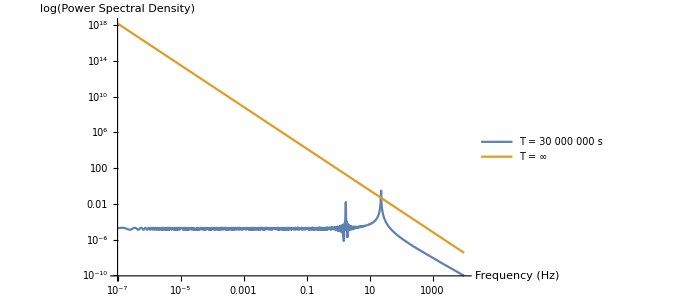

```mathematica
LogLogPlot[{approxpowerdistq[x, 30000000, 9.78*10^(-56)],  Abs[(2*Pi)^(7/6)/x^(7/6)]^2}, {x, 10^(-7), 10000}, PlotRange->{{10^(-7), 10000}, Automatic}, PlotPoints->20, AxesLabel->{HoldForm["Frequency (Hz)"],HoldForm["log(Power Spectral Density)"]}, PlotLegends->{"T = 30 000 000 s", "T = ∞"}, Ticks->{Automatic, None},BaseStyle->texStyle, LabelStyle->{Black,14}]
```

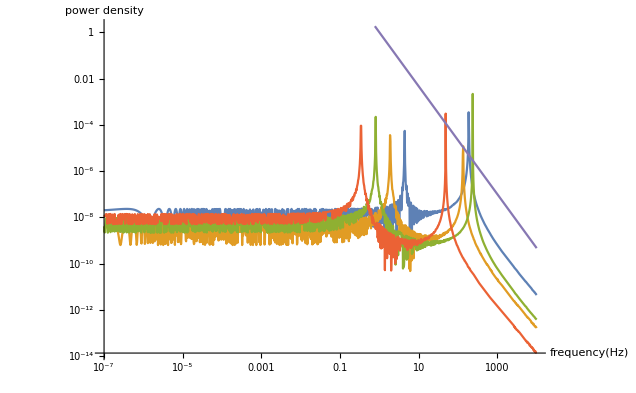

```mathematica
LogLogPlot[{approxpowerdistq[x, 3000000,0.5*9.78*10^(-56) ], approxpowerdistq[x, 30000000,0.5* 9.78*10^(-56)], approxpowerdistq[x, 300000000, 0.5*9.78*10^(-56)], approxpowerdistq[x, 3000000000,0.5* 9.78*10^(-56)], Abs[1/x^(7/6)]^2}, {x, 10^(-7), 10000}, PlotRange->{{10^(-7), 10000}, Automatic}, PlotPoints->20, AxesLabel->{HoldForm[frequency [Hz]],HoldForm[power density ]}(* PlotLegends->{"T = 30 000 000 s", "T = ∞"}*)]
```